```mathematica
Como Definir Funções
```

```mathematica
f[x_]:=x^2+3
```

":=" : A definicao da função é essa: 
“x_”:  Qualquer argumento que eu colocar dentro de f, fara o algoritmo da funcao. Por exemplo, no exemplo anterior esse argumento sera elevado a 2. Veja:

```mathematica
f[y]
```

3+y^2

```mathematica
f[3]
```

12

```mathematica
f[{1,2}]
```

{4,7}



```mathematica
plt = Plot[Sin[x], {x, 0, 2π}]
```

```mathematica
f[plt]
```

3+-Graphics-^2

```mathematica
Clear[f,x,y]
```

```mathematica
f[x_,y_]:= x^2+3y
```

```mathematica
f[1,2]
```

7

```mathematica
f[a,b]
```

a^2+3 b

Funcao composta:

```mathematica
f[x_]:= Sin[x]+7
```

```mathematica
g[x_]:=x^4
```

```mathematica
h[x_]:=g[f[x]]
```

```mathematica
h[x]
```

(7+Sin[x])^4

```mathematica
Clear[x,y,z]
```

```mathematica
CONDITIONS
```

```mathematica
f[x_/;x<0]:= -1
f[x_/;x>=0]:=x
```

```mathematica
f[2]
```

2

```mathematica
f[-3]
```

-1

```mathematica
Clear[x]
```

```mathematica
f[x_, y_]:=If[x>y, 1, 0]
```

```mathematica
f[2,1]
```

1

```mathematica
f[3, 4]
```

0

```mathematica
f[x_, y_]:=If[y>x/2,√3 y,0]
```

```mathematica
f[1, 0.7]
```

1.21244

```mathematica
f[1,0.2]
```

0

```mathematica
f[x_, y_]:=If[y<=(√(4-x^2))/2, √3 y, -√3 y+√(3*(4-x^2))]
```

```mathematica
f[0, 0.5]
```

0.866025

```mathematica
f[0, 1.7]
```

0.519615

```mathematica
f[x_]:=If[0<=x<1, 1]
f[x_]:=If[x==1,4]
```

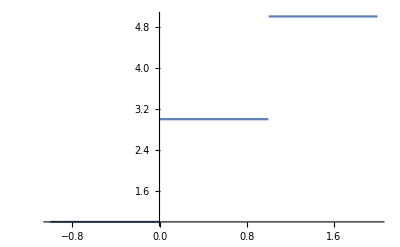

```mathematica
Plot[Piecewise[{{1, x<0},{5, x>1}, {3, 0<x<1}}], {x, -1, 2} ]
```

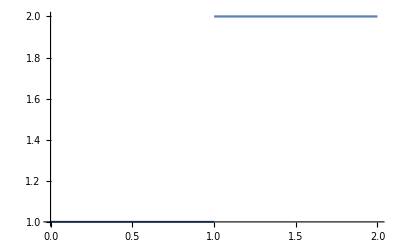

```mathematica
Plot[Piecewise[{{1, 0<=x<1}, {4, x==1}, {2, 1<x<=2}}], {x, 0, 2}]
```

```mathematica
f[x_]:=3 /; x>0
```

```mathematica
f[2]
```

3

```mathematica
f[x_]:=2/;x>0
f[x_]:=3/;x<0
```

```mathematica
f[2]
```

2

```mathematica
f[-1]
```

3

```mathematica
Element[3/4, Rationals]
```

True

```mathematica
!Element[3/4, Rationals]
```

False

! : Negação

```mathematica
x=2;
Element[x, Rationals]
```

True

```mathematica
Clear[x]
```

```mathematica
g[x_]:=5/;Element[x, Rationals]
```

```mathematica
g[2]
```

5

```mathematica
g[x_]:=x/;Element[x, Rationals]
```

```mathematica
g[3]
```

3

```mathematica
g[x_]:=x/;Element[x,Rationals]
g[x_]:=-x/;!Element[x, Rationals]
```

```mathematica
g[2]
```

2

```mathematica
g[π]
```

-π

```mathematica
Integrate[Piecewise[{{x, Element[x, Rationals]}, {-x, !Element[x,Rationals]}}], {x, -1,1}]
```

0